# Shapes II

## Eric Miller

## Prerequisites: Helper functions

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
myRegionPlot[f_,bounds_]:=RegionPlot[f,{x,bounds[[1]],bounds[[2]]},{y,bounds[[1]],bounds[[2]]},PlotPoints->60]
myRegionPlot[f_] := (bounds=RegionBounds[ImplicitRegion[f,{x,y}]];min=Min[bounds[[1]][[1]],bounds[[2]][[1]]];max=Max[bounds[[1]][[2]],bounds[[2]][[2]]];myRegionPlot[f,{min,max}])
```

```mathematica
regionIntegrate[region_,function_]:=Integrate[function,{x,y}∈ImplicitRegion[region,{x,y}]]
regionIntegrate[region_]:=regionIntegrate[region,1]
```

## Problems

### 1: Fundamental Functions

```mathematica
list={f[x],x^n,Sin[x],Cos[x],Exp[x],Log[x]}
```

{f[x],x^n,Sin[x],Cos[x],ⅇ^x,Log[x]}

```mathematica
grid=Grid[Map[TraditionalForm,Transpose[{list,Table[D[i,x],{i,list}],Table[Integrate[i,x],{i,list}]}],{2}],Frame->All]
```

f(x) | f'(x) | ∫f(x)ⅆx
x^n | n x^(n-1) | x^(n+1)/(n+1)
sin(x) | cos(x) | -cos(x)
cos(x) | -sin(x) | sin(x)
ⅇ^x | ⅇ^x | ⅇ^x
log(x) | 1/x | x log(x)-x

```mathematica
Export["grid.png",Rasterize[grid,RasterSize->600]]
```

grid.png

```mathematica
D[(x^3-1)^100,x]
```

300 x^2 (-1+x^3)^99

```mathematica
Integrate[Sqrt[2x-1],{x,0,4}]
```

1/3 (ⅈ+7 √7)

```mathematica
D[Sqrt[x](1-x),x]
```

(1-x)/(2 √x)-√x

```mathematica
Expand[Integrate[x Exp[-x],{x,1,2}]]
```

-3/ⅇ^2+2/ⅇ

```mathematica
∫_-3^3 (2-2 (x/3)^20)ⅆx
```

80/7

```mathematica
Denominator[80/7]
```

7

```mathematica
Integrate[Sqrt[1-x^2],{x,-1,1}]
```

π/2

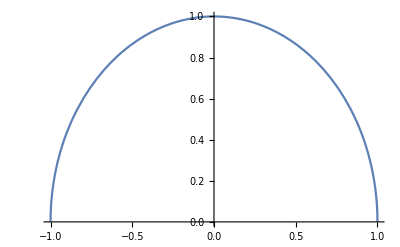

```mathematica
Plot[Sqrt[1-x^2],{x,-1,1}]
```

### 9. Function family

```mathematica
y1[x_,n_]:=x^n
y2[x_]:=d
```

```mathematica
integral = Simplify[Assuming[n>=1,Integrate[d-x^n,{x,0,d^(1/n)}]]]
```

(d^(1+1/n) n)/(1+n)

```mathematica
Solve[{integral==100,n==2},d]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{d→100^(-1/(-1-1/n)) (n/(1+n))^(-n/(1+n))}}

```mathematica
(d^(1/n))^n
```

(d^(1/n))^n

```mathematica
Solve[y1==y2,x]
```

{}

```mathematica
First[{{n->Log[d]/Log[x]}}]
```

{3→Log[d]/Log[x]}

```mathematica
area[n_,d_]:=(d^(1+1/n) n)/(1+n)
```

```mathematica
Manipulate[LogLogPlot[area[nn,d],{d,1,100},AxesLabel->{d,"Area"},PlotLabel->TraditionalForm[HoldForm[TraditionalForm[n]]==Evaluate[nn]]],{nn,1,10,1}]
```

```mathematica
Plot3D[area[n,d],{n,1,3},{d,1,100},AxesLabel->{"n","d","area"},PlotRange->All]
```

-Graphics3D-

```mathematica
f:=x^2 sin(x y^2)
```

```mathematica
D[f,x]
D[f,y]
```

x^2 y^2 Cos[x y^2]+2 x Sin[x y^2]

2 x^3 y Cos[x y^2]

```mathematica
D[f,x,x]
D[f,x,y]
D[f,y,x]
D[f,y,y]
```

4 x y^2 Cos[x y^2]+2 Sin[x y^2]-x^2 y^4 Sin[x y^2]

6 x^2 y Cos[x y^2]-2 x^3 y^3 Sin[x y^2]

6 x^2 y Cos[x y^2]-2 x^3 y^3 Sin[x y^2]

2 x^3 Cos[x y^2]-4 x^4 y^2 Sin[x y^2]

### 14. Regions of Integration

```mathematica
region=x>=0&&x<=1&&y>=0&&y<=x
```

x≥0&&x≤1&&y≥0&&y≤x

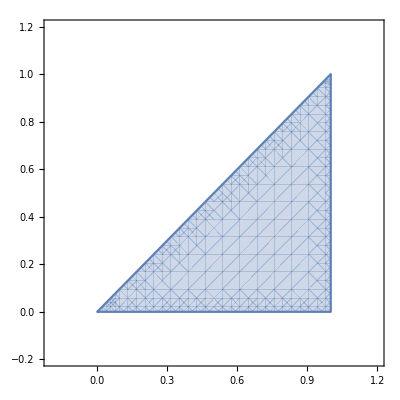

```mathematica
myRegionPlot[region,{-.2,1.2}]
```

```mathematica
regionIntegrate[region]
```

1/2

```mathematica
regions={x>=0&&x<=1&&y>=0&&y<=x,
x>=0&&x≤Pi/2&&y>=0&&y≤Sin[x],
x≥1&&x≤2&&y>=0&&y≤Log[x]}
```

{x≥0&&x≤1&&y≥0&&y≤x,x≥0&&x≤π/2&&y≥0&&y≤Sin[x],x≥1&&x≤2&&y≥0&&y≤Log[x]}

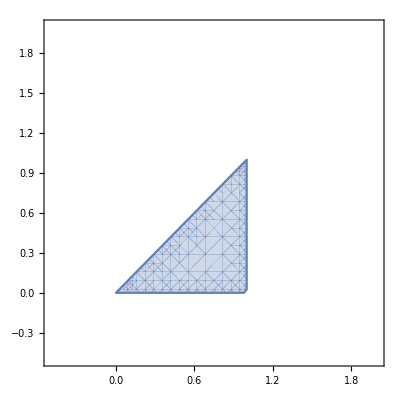
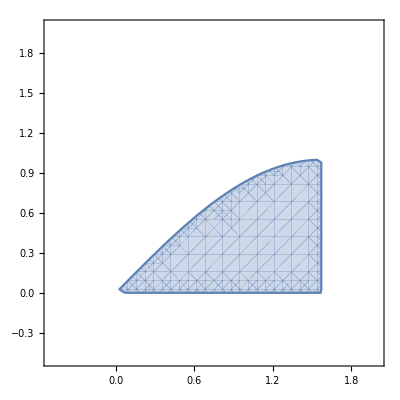
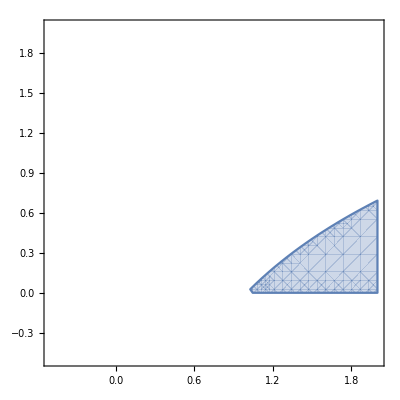
x≥0∧x≤1∧y≥0∧y≤x | -Graphics- | 1/2
x≥0∧x≤π/2∧y≥0∧y≤sin(x) | -Graphics- | 1
x≥1∧x≤2∧y≥0∧y≤log(x) | -Graphics- | log(4)-1

```mathematica
Grid[Table[{TraditionalForm@i,myRegionPlot[i,{-.5,2}],TraditionalForm@regionIntegrate[i]},{i,regions}],Dividers->All]
```

```mathematica
Export["table2.png",%]
```

table2.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["table2.png"]]]
```

```mathematica
regions2={x≥y&&x≤2-y&&y≥0&&y≤1,
x≥y/2&&x≤2&&y>=0&&y≤4,
x≥y&&x≤E^y&&y>=0&&y≤1}
```

{x≥y&&x≤2-y&&y≥0&&y≤1,x≥y/2&&x≤2&&y≥0&&y≤4,x≥y&&x≤ⅇ^y&&y≥0&&y≤1}

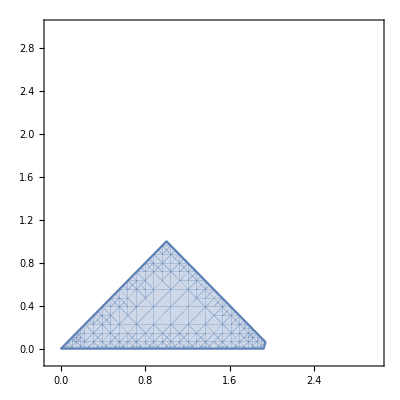
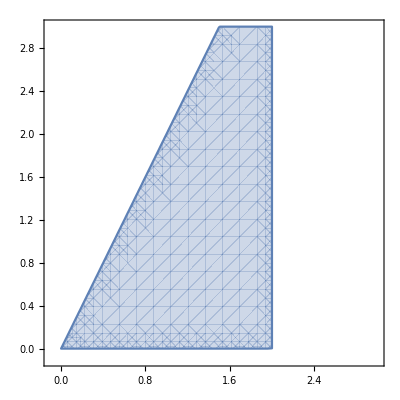
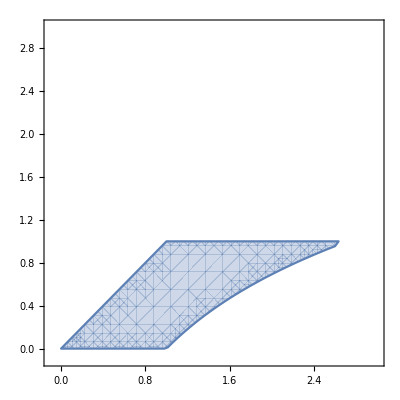
x≥y∧x≤2-y∧y≥0∧y≤1 | -Graphics- | 1
x≥y/2∧x≤2∧y≥0∧y≤4 | -Graphics- | 4
x≥y∧x≤ⅇ^y∧y≥0∧y≤1 | -Graphics- | 1/2 (2 ⅇ-3)

```mathematica
Grid[Table[{TraditionalForm@i,myRegionPlot[i,{-.1,3}],TraditionalForm@regionIntegrate[i]},{i,regions2}],Dividers->All]
```

```mathematica
Export["Grid3.png",%]
```

Grid3.png

### 16. Complex region

#### The hard way

10/3

#### The easy way

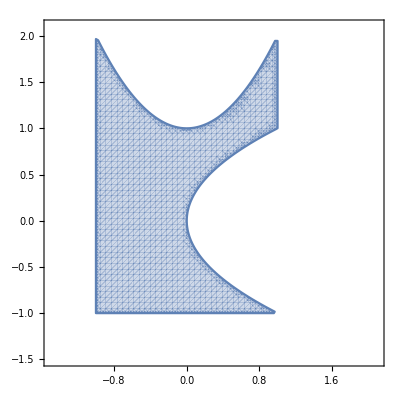
x≥-1∧x≤1∧y≥-1∧y≤x^2+1∧x<y^2 | -Graphics- | 10/3

```mathematica
Grid[Table[{TraditionalForm@i,myRegionPlot[i,{-1.5,2.1}],TraditionalForm@regionIntegrate[i]},{i,{x≥-1&&x≤1&&y≥-1&&y≤1+x^2&&x<y^2}}],Dividers->All]
```

```mathematica
Export["grid4.png",%]
```

grid3.png

### 17. 3D regions

```mathematica
regions={{4y/(x^3+2),1≤x≤2&&0≤y≤2x}, {x Cos[y],0≤x≤1&&0≤y≤x^2}}
```

{{(4 y)/(2+x^3),1≤x≤2&&0≤y≤2 x},{x Cos[y],0≤x≤1&&0≤y≤x^2}}

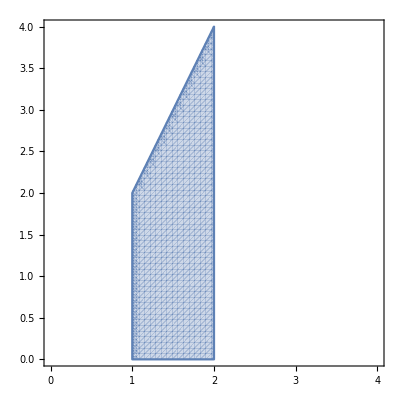

```mathematica
myRegionPlot[1≤x≤2&&0≤y≤2x]
```

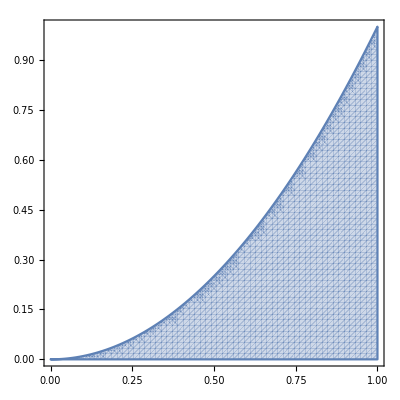
(4 y)/(x^3+2) | -Graphics- | 8/3 log(10/3) | 3.21059
x cos(y) | -Graphics- | sin^2(1/2) | 0.229849

grid5.png

```mathematica
output=Grid[Table[{TraditionalForm@i[[1]],myRegionPlot[i[[2]]],integral=Simplify@regionIntegrate[i[[2]],i[[1]]];TraditionalForm@integral,N@integral},{i,regions}],Dividers->All]
Export["grid5.png",output]
```

### 18. Solids

```mathematica
regions={x≥0&&y≥0&&z≥0&&x+y+z≤1,
0<z<x^2+y^2 && y≥ x^2&&x≥y^2};
```

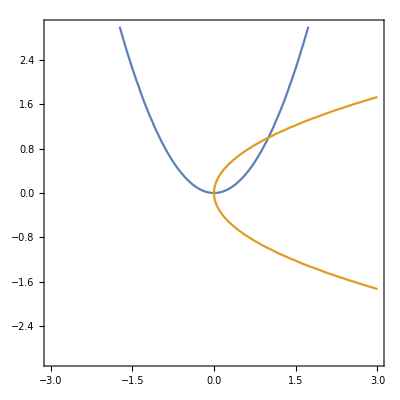

```mathematica
ContourPlot[{y==x^2,x==y^2},{x,-3,3},{y,-3,3}]
```

```mathematica
Integrate[1,{x,y,z}∈ImplicitRegion[regions[[1]],{x,y,z}]]
RegionPlot3D[regions[[1]],{x,-.2,1.2},{y,-.2,1.2},{z,-.2,1.2},PlotPoints->100]
```

1/6

-Graphics3D-

```mathematica
Integrate[1,{x,y,z}∈ImplicitRegion[regions[[2]],{x,y,z}]]
RegionPlot3D[regions[[2]],{x,-.2,1},{y,-.2,1},{z,-.2,2},PlotPoints->100]
```

6/35

-Graphics3D-

### 19. Solids

```mathematica
regions={0<z<1&&0<x<z&&0<y<x+z,
0<z<x^2+y^2 && y≥ x^2&&x≥y^2};
```

```mathematica
ContourPlot[{y==x^2,x==y^2},{x,-3,3},{y,-3,3}]
```

-Graphics-

```mathematica
Integrate[1,{x,y,z}∈ImplicitRegion[regions[[1]],{x,y,z}]]
RegionPlot3D[regions[[1]],{x,-.2,1.2},{y,-.2,1.2},{z,-.2,1.2},PlotPoints->100]
```

1/6

-Graphics3D-

```mathematica
Integrate[1,{x,y,z}∈ImplicitRegion[regions[[2]],{x,y,z}]]
RegionPlot3D[regions[[2]],{x,-.2,1},{y,-.2,1},{z,-.2,2},PlotPoints->100]
```

6/35

-Graphics3D-